```mathematica
cellvideo = "/home/tom/complex/MP2/Gifs/jbc.M112.437913-21.gif";
```

```mathematica
frames = Import[cellvideo];
```

```mathematica
a=frames[[2]];
```

```mathematica
dims=ImageDimensions[frames⟦2⟧]
splitChannels=Flatten[Map[(ImagePartition[#, {dims⟦1⟧/2,dims⟦2⟧}])&, frames],1];
b = splitChannels[[2]];
Export["/home/tom/complex/MP2/EndOfWeek2/rawsampleframe.png",GraphicsGrid[{{a}},ImageSize->800],"PNG"]
Export["/home/tom/complex/MP2/EndOfWeek2/splitampleframe.png",GraphicsGrid[{b},ImageSize->800],"PNG"]
```

{1024,512}

/home/tom/complex/MP2/EndOfWeek2/rawsampleframe.png

/home/tom/complex/MP2/EndOfWeek2/splitampleframe.png

```mathematica
(*averageImage=Image[Mean[Map[ImageData[#]&,splitChannels⟦All,1⟧]]] *)
```

```mathematica
(*x = ImageData[splitChannels[[1]]]
Image[Mean[x]]*)
averageImage=Image[Mean[Map[ImageData[#]&,splitChannels⟦All,1⟧]]]
```

-Graphics-

```mathematica
detectedCells = MorphologicalComponents[averageImage,0.07];
cleanDetectedCells = SelectComponents[detectedCells,(#Area > 100) &];
Colorize[detectedCells]
Colorize[cleanDetectedCells]
Length[detectedCells[[1]]]
```

-Graphics-

-Graphics-

512

```mathematica
Export["/home/tom/complex/MP2/EndOfWeek2/morphcomp.png",GraphicsGrid[{{averageImage,Colorize[detectedCells],Colorize[cleanDetectedCells]},{"(a)","(b)","(c)"}},ImageSize->1000,Alignment->{Center,Top}],"PNG"]
```

/home/tom/complex/MP2/EndOfWeek2/morphcomp.png

```mathematica
cells=ComponentMeasurements[cleanDetectedCells,{"Centroid","SemiAxes","Orientation"}];
```

```mathematica
labels= Flatten[Table[{Yellow, Text[cells⟦i,1⟧, cells⟦i,2,1⟧]}, {i, Length[cells]}]];
ImageCompose[HighlightImage[averageImage,Colorize[cleanDetectedCells]],Graphics[labels]]
```

-Graphics-

```mathematica
cells;
```

```mathematica
boundingEllipses = Map[Rotate[Disk[#[[1]],#[[2]]],#[[3]]]&,Table[{cells[[i]][[2]][[1]],cells[[i]][[2]][[2]],cells[[i]][[2]][[3]]},{i, Length[cells]}]];
labels= Flatten[Table[{Yellow, Text[cells⟦i,1⟧, cells⟦i,2,1⟧]}, {i, Length[cells]}]];

ImageCompose[HighlightImage[averageImage,boundingEllipses],Graphics[labels]]
Export["/home/tom/complex/MP2/EndOfWeek2/boundingellipses.png",ImageCompose[HighlightImage[averageImage,boundingEllipses],Graphics[labels]], "PNG"]
```

-Graphics-

/home/tom/complex/MP2/EndOfWeek2/boundingellipses.png

```mathematica
cellIntensities = Table[Map[{#[[1]],#[[2]]}&,ComponentMeasurements[{cleanDetectedCells,splitChannels⟦i,1⟧},"MeanIntensity"]],{i,Length[splitChannels]}]
```

{{{2,0.136146},{3,0.12944},{5,0.0959002},{6,0.187471},{7,0.201548},{9,0.103854},{10,0.197271},{11,0.258571},{12,0.104381},{13,0.192126},{15,0.133636},{17,0.167205},{18,0.176068},{19,0.269923},{20,0.142808},152,{222,0.260512},{223,0.163117},{225,0.171375},{226,0.211958},{227,0.146481},{228,0.182239},{229,0.204045},{230,0.0883829},{231,0.0659457},{235,0.189625},{237,0.15327},{238,0.137549},{239,0.0607182},{240,0.127324},{241,0.147347}},303,{1}}
 |  |  |  |

```mathematica
mainHeader = {"Cell", "Av. Intensity per frame(time/s)"};
frameTimes = Table[1.1*i,{i,0,Length[frames]-1}];
subHeader = Join[{""},frameTimes];
outData = Table[Join[{Transpose[cellIntensities][[i]][[1]][[1]]},Map[#[[2]]&,Transpose[cellIntensities][[i]]]],{i,Length[cells]}];
results = Join[{mainHeader},{frameTimes},outData];
```

```mathematica
Export["/home/tom/complex/MP2/results/intensities.csv",results,"CSV"]
```

/home/tom/complex/MP2/results/intensities.csv

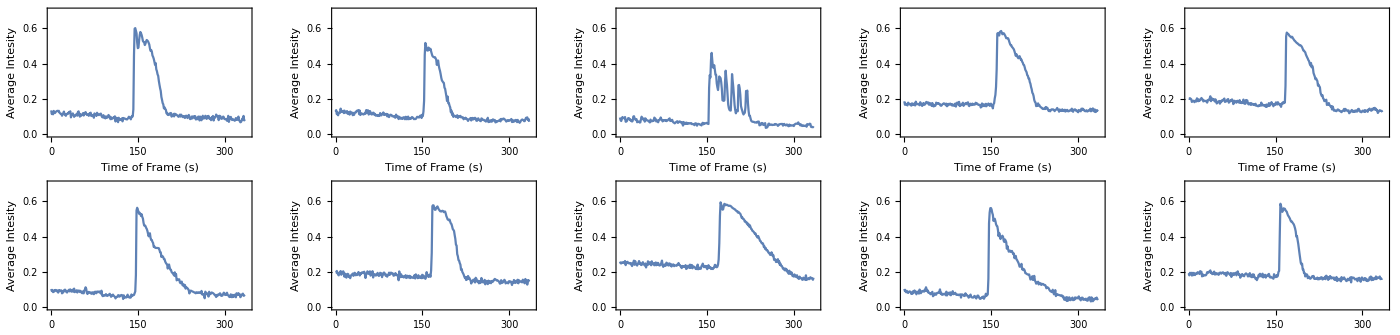

/home/tom/complex/MP2/EndOfWeek2/sampleIntPlots.png

```mathematica
Partition[Riffle[frameTimes,Map[#[[2]]&,Transpose[cellIntensities][[11]]]],2];
ListPlot[Partition[Riffle[frameTimes,Map[#[[2]]&,Transpose[cellIntensities][[11]]]],2],PlotRange->{{-0,340},{0,0.7}},Frame-> True,FrameLabel->{"Time of Frame (s)","Average Intesity"}];
plots = Table[ListLinePlot[Partition[Riffle[frameTimes,Map[#[[2]]&,Transpose[cellIntensities][[i]]]],2],PlotRange->{{-0,340},{0,0.7}}, Frame -> True,FrameLabel->{"Time of Frame (s)","Average Intesity"}],{i,10}];
GraphicsGrid[Partition[plots,5],ImageSize->1400]
Export["/home/tom/complex/MP2/EndOfWeek2/sampleIntPlots.png",GraphicsGrid[Partition[plots,5],ImageSize->1400],"PNG"]
```